### Setting up board

#### Global variables

Indexing

```mathematica
MINETYPEI=1;
REVEALORNOT = 2;
NEIGHBORDATAI=3;
TRIPOINTI=4;
NMINESI=5;
ISFLAGGEDI = 6;
```

Mine and other attributes

```mathematica
MINE = 1;
NOTMINE = 0;
NOTREVEALED = 0;
REVEALED = 1;
ISFLAGGED = True;
NOTFLAGGED = False;
```

#### Getters

```mathematica
getTileType[board_,sector_,row_,column_]:=board⟦sector,row,column,1⟧
```

```mathematica
getTilePoints[board_,sector_,row_,column_]:=board⟦sector,row,column,2⟧
```

```mathematica
getNeighborPos[board_,sector_,row_,column_]:=board⟦sector,row,column,3⟧
```

```mathematica
(*Returns tile data for structured board*)
getTile[board_,listPos_]:=board⟦listPos⟦1⟧,listPos⟦2⟧,listPos⟦3⟧⟧
```

#### Mine setup

```mathematica
neighborsWith0[board_, section_,row_,column_]:=Select[board⟦section,row,column,3⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,1⟧===0&&board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧===0 &]
```

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,factor_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles,remainingMineCount,tile,skeletons,neighbors},

remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
(*zeros are  not mines and 1s are mines*)
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{MINE,NOTMINE}];
If[tile===MINE,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];

Return [lst]
]
```

```mathematica
setupMines[3,0.25]
```

{{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{1,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{1,0}},{{1,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{1,0},{0,0}},{{1,0},{0,0},{0,0},{0,0},{1,0}}},{{{1,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{1,0},{1,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,0},{0,0}}},{{{1,0}},{{1,0},{1,0},{1,0}},{{0,0},{0,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{1,0},{1,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}}

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,factor_,offLimits_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles,remainingMineCount,tile,skeletons,neighbors},

remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
(*zeros are  not mines and 1s are mines*)
If[MemberQ[offLimits,{section,row,numOfTiles}],AppendTo[lst⟦section,row⟧,0];tiles--;Continue[]];
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{MINE,NOTMINE}];
If[tile===MINE,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];

Return [lst]
]
```

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{(*This constructs the zigzag shape of the triangles*)
zigzag=Riffle[
Table[N@{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[N@{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
(*Take advantage of the zigzag shape to construct triangles*)
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

```mathematica
constructTiledTriangleRow[5,{0,0}]
```

{{{-1.14805,0.92388},{-0.765367,0.},{-0.382683,0.92388}},{{-0.765367,0.},{-0.382683,0.92388},{0.,0.}},{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}},{{0.,0.},{0.382683,0.92388},{0.765367,0.}},{{0.382683,0.92388},{0.765367,0.},{1.14805,0.92388}}}

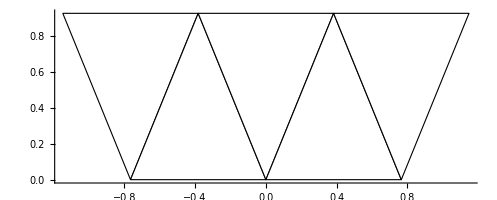

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

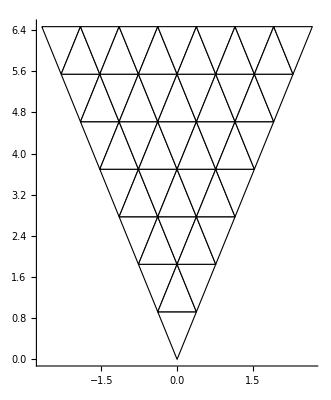

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles.
The return structure is structured the same way as a regular board, except this only gives tile corner coordinates
*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

```mathematica
createBoardSkeleton[3]
```

{{{{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}}},{{{-0.765367,1.84776},{-0.382683,0.92388},{0.,1.84776}},{{-0.382683,0.92388},{0.,1.84776},{0.382683,0.92388}},{{0.,1.84776},{0.382683,0.92388},{0.765367,1.84776}}},{{{-1.14805,2.77164},{-0.765367,1.84776},{-0.382683,2.77164}},{{-0.765367,1.84776},{-0.382683,2.77164},{0.,1.84776}},{{-0.382683,2.77164},{0.,1.84776},{0.382683,2.77164}},{{0.,1.84776},{0.382683,2.77164},{0.765367,1.84776}},{{0.382683,2.77164},{0.765367,1.84776},{1.14805,2.77164}}}},{{{{0.382683,0.92388},{0.,0.},{0.92388,0.382683}}},{{{0.765367,1.84776},{0.382683,0.92388},{1.30656,1.30656}},{{0.382683,0.92388},{1.30656,1.30656},{0.92388,0.382683}},{{1.30656,1.30656},{0.92388,0.382683},{1.84776,0.765367}}},{{{1.14805,2.77164},{0.765367,1.84776},{1.68925,2.23044}},{{0.765367,1.84776},{1.68925,2.23044},{1.30656,1.30656}},{{1.68925,2.23044},{1.30656,1.30656},{2.23044,1.68925}},{{1.30656,1.30656},{2.23044,1.68925},{1.84776,0.765367}},{{2.23044,1.68925},{1.84776,0.765367},{2.77164,1.14805}}}},{{{{0.92388,0.382683},{0.,0.},{0.92388,-0.382683}}},{{{1.84776,0.765367},{0.92388,0.382683},{1.84776,0.}},{{0.92388,0.382683},{1.84776,0.},{0.92388,-0.382683}},{{1.84776,0.},{0.92388,-0.382683},{1.84776,-0.765367}}},{{{2.77164,1.14805},{1.84776,0.765367},{2.77164,0.382683}},{{1.84776,0.765367},{2.77164,0.382683},{1.84776,0.}},{{2.77164,0.382683},{1.84776,0.},{2.77164,-0.382683}},{{1.84776,0.},{2.77164,-0.382683},{1.84776,-0.765367}},{{2.77164,-0.382683},{1.84776,-0.765367},{2.77164,-1.14805}}}},{{{{0.92388,-0.382683},{0.,0.},{0.382683,-0.92388}}},{{{1.84776,-0.765367},{0.92388,-0.382683},{1.30656,-1.30656}},{{0.92388,-0.382683},{1.30656,-1.30656},{0.382683,-0.92388}},{{1.30656,-1.30656},{0.382683,-0.92388},{0.765367,-1.84776}}},{{{2.77164,-1.14805},{1.84776,-0.765367},{2.23044,-1.68925}},{{1.84776,-0.765367},{2.23044,-1.68925},{1.30656,-1.30656}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},{{1.30656,-1.30656},{1.68925,-2.23044},{0.765367,-1.84776}},{{1.68925,-2.23044},{0.765367,-1.84776},{1.14805,-2.77164}}}},{{{{0.382683,-0.92388},{0.,0.},{-0.382683,-0.92388}}},{{{0.765367,-1.84776},{0.382683,-0.92388},{0.,-1.84776}},{{0.382683,-0.92388},{0.,-1.84776},{-0.382683,-0.92388}},{{0.,-1.84776},{-0.382683,-0.92388},{-0.765367,-1.84776}}},{{{1.14805,-2.77164},{0.765367,-1.84776},{0.382683,-2.77164}},{{0.765367,-1.84776},{0.382683,-2.77164},{0.,-1.84776}},{{0.382683,-2.77164},{0.,-1.84776},{-0.382683,-2.77164}},{{0.,-1.84776},{-0.382683,-2.77164},{-0.765367,-1.84776}},{{-0.382683,-2.77164},{-0.765367,-1.84776},{-1.14805,-2.77164}}}},{{{{-0.382683,-0.92388},{0.,0.},{-0.92388,-0.382683}}},{{{-0.765367,-1.84776},{-0.382683,-0.92388},{-1.30656,-1.30656}},{{-0.382683,-0.92388},{-1.30656,-1.30656},{-0.92388,-0.382683}},{{-1.30656,-1.30656},{-0.92388,-0.382683},{-1.84776,-0.765367}}},{{{-1.14805,-2.77164},{-0.765367,-1.84776},{-1.68925,-2.23044}},{{-0.765367,-1.84776},{-1.68925,-2.23044},{-1.30656,-1.30656}},{{-1.68925,-2.23044},{-1.30656,-1.30656},{-2.23044,-1.68925}},{{-1.30656,-1.30656},{-2.23044,-1.68925},{-1.84776,-0.765367}},{{-2.23044,-1.68925},{-1.84776,-0.765367},{-2.77164,-1.14805}}}},{{{{-0.92388,-0.382683},{0.,0.},{-0.92388,0.382683}}},{{{-1.84776,-0.765367},{-0.92388,-0.382683},{-1.84776,0.}},{{-0.92388,-0.382683},{-1.84776,0.},{-0.92388,0.382683}},{{-1.84776,0.},{-0.92388,0.382683},{-1.84776,0.765367}}},{{{-2.77164,-1.14805},{-1.84776,-0.765367},{-2.77164,-0.382683}},{{-1.84776,-0.765367},{-2.77164,-0.382683},{-1.84776,0.}},{{-2.77164,-0.382683},{-1.84776,0.},{-2.77164,0.382683}},{{-1.84776,0.},{-2.77164,0.382683},{-1.84776,0.765367}},{{-2.77164,0.382683},{-1.84776,0.765367},{-2.77164,1.14805}}}},{{{{-0.92388,0.382683},{0.,0.},{-0.382683,0.92388}}},{{{-1.84776,0.765367},{-0.92388,0.382683},{-1.30656,1.30656}},{{-0.92388,0.382683},{-1.30656,1.30656},{-0.382683,0.92388}},{{-1.30656,1.30656},{-0.382683,0.92388},{-0.765367,1.84776}}},{{{-2.77164,1.14805},{-1.84776,0.765367},{-2.23044,1.68925}},{{-1.84776,0.765367},{-2.23044,1.68925},{-1.30656,1.30656}},{{-2.23044,1.68925},{-1.30656,1.30656},{-1.68925,2.23044}},{{-1.30656,1.30656},{-1.68925,2.23044},{-0.765367,1.84776}},{{-1.68925,2.23044},{-0.765367,1.84776},{-1.14805,2.77164}}}}}

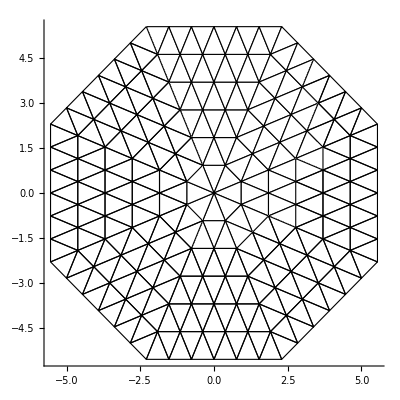

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[6]]},Axes->True]
```

#### Neighbors setup (point comparison)

We use an association to figure out which triangles share points. The coordinates will be rounded by a 1/100 to accommodate a reasonable floating point error.
We then handle adjacencies by outer edge connection as a separate case

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
roundCoordHundredths[coord_]:=Map[Round[#*100]/100.&,coord]
```

```mathematica
(*Returns an association. Each key is a point rounded to the hundredths, and the values are lists of triangles which have that point*)
findSharedPoints[trianglesCoords_]:=
Module[{pointsAssociations=Association[]},

Do[
(*Point is not yet in association*)
If[MissingQ@pointsAssociations[roundCoordHundredths[point]],
AssociateTo[pointsAssociations,roundCoordHundredths[point]->{}];
];
(*Add point to association*)
AssociateTo[pointsAssociations,roundCoordHundredths[point]->Append[pointsAssociations[roundCoordHundredths[point]],{sectorI,rowI,tileI}]];
,{sectorI,Length@trianglesCoords}
,{rowI,Length@trianglesCoords⟦sectorI⟧}
,{tileI,Length@trianglesCoords⟦sectorI,rowI⟧}
,{point,trianglesCoords⟦sectorI,rowI,tileI⟧}
];
Return[pointsAssociations]
]
```

```mathematica
Length@createBoardSkeleton[3]⟦1⟧
```

3

```mathematica
findSharedPoints[createBoardSkeleton[2]]
```

<|{-0.38,0.92}→{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3}},{0.,0.}→{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1}},{0.38,0.92}→{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},{-0.77,1.85}→{{1,2,1},{8,2,3}},{0.,1.85}→{{1,2,1},{1,2,2},{1,2,3}},{0.77,1.85}→{{1,2,3},{2,2,1}},{0.92,0.38}→{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},{1.31,1.31}→{{2,2,1},{2,2,2},{2,2,3}},{1.85,0.77}→{{2,2,3},{3,2,1}},{0.92,-0.38}→{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},{1.85,0.}→{{3,2,1},{3,2,2},{3,2,3}},{1.85,-0.77}→{{3,2,3},{4,2,1}},{0.38,-0.92}→{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},{1.31,-1.31}→{{4,2,1},{4,2,2},{4,2,3}},{0.77,-1.85}→{{4,2,3},{5,2,1}},{-0.38,-0.92}→{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},{0.,-1.85}→{{5,2,1},{5,2,2},{5,2,3}},{-0.77,-1.85}→{{5,2,3},{6,2,1}},{-0.92,-0.38}→{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},{-1.31,-1.31}→{{6,2,1},{6,2,2},{6,2,3}},{-1.85,-0.77}→{{6,2,3},{7,2,1}},{-0.92,0.38}→{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},{-1.85,0.}→{{7,2,1},{7,2,2},{7,2,3}},{-1.85,0.77}→{{7,2,3},{8,2,1}},{-1.31,1.31}→{{8,2,1},{8,2,2},{8,2,3}}|>

```mathematica
countMines[mineLst_,neighborLst_,sector_,row_,tile_]:=Module[
{},
Return[Length@Select[neighborLst⟦sector,row,tile,1⟧,mineLst⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧==1&]]
]
```

```mathematica
(*Returns the neighbors of each tile in the tiling given the coordinates of the tiles.
Returns in the same form as the regular board, but only giving the neighbor data.
*)
setupNeighbors[mineLst_,trianglesCoords_]:=
Module[
{pointsSharing=findSharedPoints[trianglesCoords],
neighborLst=Table[Table[Table[{{}},{tile,row}],{row,sector}],{sector,trianglesCoords}],
POI,
countMinesLst
},
POI=Keys[pointsSharing];
(*Add adjacent triangles*)
Do[
If[triangle1==triangle2||
MemberQ[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2]||
mineLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧⟧,Continue[]];
AppendTo[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2];
,{point,POI}
,{triangle1,pointsSharing[point]}
,{triangle2,pointsSharing[point]}
];
setupNeighborsConnectEdges[neighborLst];
(*All vertices of octagon coincide into a point*)
Do[
If[{sector,tile}=={otherSector,otherTile},Continue[]];
AppendTo[neighborLst⟦sector,Length@mineLst⟦1⟧,tile,1⟧,{otherSector,Length@mineLst⟦1⟧,otherTile}]
,{sector,Length@mineLst}
,{tile,{1,2Length@mineLst⟦sector⟧-1}}
,{otherSector,Length@mineLst}
,{otherTile,{1,2Length@mineLst⟦otherSector⟧-1}}
];
Do[
neighborLst⟦sector,row,tile,1⟧=DeleteDuplicates[neighborLst⟦sector,row,tile,1⟧];
AppendTo[neighborLst⟦sector,row,tile⟧,countMines[mineLst,neighborLst,sector,row,tile]]
,{sector,Length@neighborLst}
,{row,Length@neighborLst⟦sector⟧}
,{tile,Length@neighborLst⟦sector,row⟧}
];
Return[neighborLst];
]
```

```mathematica
SetAttributes[setupNeighborsConnectEdges,HoldFirst]
setupNeighborsConnectEdges[existingLst_]:=Module[
{},
setupNeighborsConnectSectorPairs[existingLst,1,3];
setupNeighborsConnectSectorPairs[existingLst,2,4];
setupNeighborsConnectSectorPairs[existingLst,5,7];
setupNeighborsConnectSectorPairs[existingLst,6,8];
setupNeighborsConnectSectorPairs[existingLst,3,1];
setupNeighborsConnectSectorPairs[existingLst,4,2];
setupNeighborsConnectSectorPairs[existingLst,7,5];
setupNeighborsConnectSectorPairs[existingLst,8,6];

]
```

```mathematica
SetAttributes[setupNeighborsConnectSectorPairs,HoldFirst]
setupNeighborsConnectSectorPairs[existingLst_,sector_,otherSector_]:=Module[
{numRows=Length@existingLst⟦1⟧,tile},
(*"up" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,2,2numRows-2,2}
,{otherTile,2numRows-tile-1,2numRows-tile+1}
];
(*"Down" pointing triangles*)
Do[
addNeighbor[existingLst⟦sector,numRows,tile,1⟧,numRows,otherSector,numRows,otherTile]
,{tile,1,2numRows-1,2}
,{otherTile,2numRows-tile-2,2numRows-tile+2}
];
]
```

```mathematica
bb=setupNeighbors[setupMines[3,0.25],createBoardSkeleton[2]]
```

{{{{{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{1,2,3},{2,2,1},{2,2,2}},0}},{{{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,2,3}},1},{{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},1},{{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1}},1}}},{{{{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2}},3}},{{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{2,2,3}},1},{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},2},{{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1}},1}}},{{{{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2}},0}},{{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{3,2,3}},2},{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},3},{{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1}},0}}},{{{{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2}},5}},{{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{4,2,3}},0},{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},3},{{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1}},1}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2}},5}},{{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{5,2,3}},0},{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},3},{{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2}},0}},{{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{6,2,3}},0},{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},0},{{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}},4}},{{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{7,2,3}},2},{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},2},{{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1}},0}}},{{{{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},3}},{{{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{8,2,3}},0},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},1},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,1}},1}}}}

#### display functions

```mathematica
(*Displays entire board using table to go through sector row and column*)
displayBoard[board_]:= Table[graphicsAtTile[board,sector,row,column],{sector,Length@board},{row,Length@board⟦sector⟧},{column,Length@board⟦sector,row⟧}]
```

```mathematica
(*Graphics for each tile. checks if mine and if revealed and based off of that, you have text and color*)
graphicsAtTile[board_,sector_,row_,column_]:=Module[
	{tile = board⟦sector,row,column⟧},
		{
		EdgeForm[{Thickness[Large],Black}],{colorAtTile[board,sector,row,column],Triangle[tile⟦TRIPOINTI⟧]},
		If[tile⟦REVEALORNOT⟧==REVEALED,Text[Style[tile⟦NMINESI⟧,FontSize->16,FontColor->White],triangleCentroid[tile⟦TRIPOINTI⟧]],Text["",triangleCentroid[tile⟦TRIPOINTI⟧]]]
		}
]
```

```mathematica
colorAtTile[board_,sector_,row_,column_]:= Module[
{tile = board⟦sector,row,column⟧},
	If[tile⟦REVEALORNOT⟧==REVEALED,
		If[tile⟦MINETYPEI⟧ == MINE,
			Return[Red],
			Return[Blue]
		]
		,
		If[tile⟦ISFLAGGEDI⟧ == ISFLAGGED,
			Return[Orange],
			Return[Gray]
		]
	]
]
```

#### Putting it all together

Combine the data for each tile into a single list.

```mathematica
triangleCentroid[triangleCoords_]:=RegionCentroid[Triangle[triangleCoords]]
```

```mathematica
boardSetUp[numOfRows_,mineFactor_,clickedTile_]:=Module[
{minesData=setupMines[numOfRows,mineFactor],
triangleCoords=createBoardSkeleton[numOfRows],
neighborData,
minesOffLimits,
curEqVarMap=1
},
neighborData=setupNeighbors[minesData,triangleCoords];
minesOffLimits=Append[neighborData⟦clickedTile⟦1⟧,clickedTile⟦2⟧,clickedTile⟦3⟧,1⟧,clickedTile];
minesData=setupMines[numOfRows,mineFactor,minesOffLimits];
neighborData=setupNeighbors[minesData,triangleCoords];
Return[
Table[
Table[
Table[
{minesData⟦sectorI,rowI,tileI⟧,
NOTREVEALED,
neighborData⟦sectorI,rowI,tileI,1⟧,
triangleCoords⟦sectorI,rowI,tileI⟧,
If[minesData⟦sectorI⟧⟦rowI⟧⟦tileI⟧ == 0,neighborData⟦sectorI,rowI,tileI,2⟧,""],
NOTFLAGGED
}
,{tileI,1,Length@minesData⟦sectorI,rowI⟧}
]
,{rowI,1,Length@minesData⟦sectorI⟧}
]
,{sectorI,1,8}
]
]
]
```

```mathematica
colorAtTile[board,1,1,1]
```

GrayLevel[0.5]

```mathematica
board=boardSetUp[5,0.25,{5,5,1}];
```

#### Setting the Game Up

```mathematica
board=boardSetUp[5,0.25,{1,5,1}];
type = "Reveal";
flag = 99;
count = 0;
boardGraphics = displayBoard[board];
play[board,boardGraphics]
```

Flags Left: 
Revealed Tiles: 

Randomize
{,Rows: }
{,Mine Density: }

Mine

Mine

Mine

```mathematica
startTime=AbsoluteTime[]
AbsoluteTime[]-startTime
```

3.8253395424216567×10^9

0.0061159

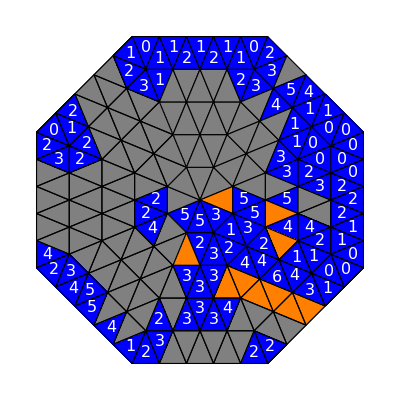

0.2646

```mathematica
startTime=AbsoluteTime[];
Graphics[boardGraphics]
AbsoluteTime[]-startTime
```

```mathematica
board⟦4,3,3⟧
```

{1,0,{{4,2,1},{4,2,2},{4,2,3},{4,3,2},{4,3,4},{4,3,1},{4,4,2},{4,4,3},{4,4,4},{4,3,5},{4,4,5},{4,4,6}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},,False}

```mathematica
Button[type,type++]
```

6